```mathematica
data=Table[x->Sin[x]+RandomVariate[NormalDistribution[0,.15]],{x,-2π,2π,.2}];
```

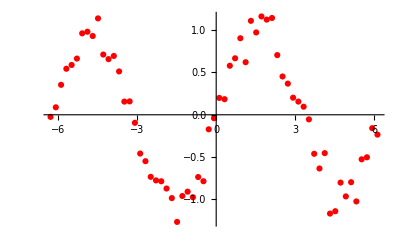

```mathematica
plot=ListPlot[List@@@data,PlotStyle->Red]
```

```mathematica
net=NetChain[{150,Tanh,150,Tanh,1},"Input"->"Scalar","Output"->"Scalar"];
net1=NetTrain[net,data,Method->"ADAM"]
```

NetChain[<>]

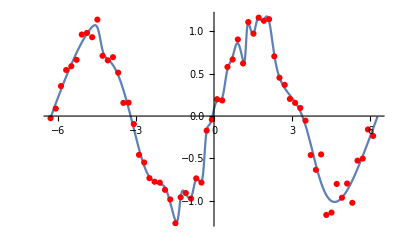

```mathematica
b=Show[Plot[net1[x],{x,-2π,2π}],plot]
Export[NotebookDirectory[]<>"overfitted_data"<>".png",b,ImageResolution->150];
```

```mathematica
data=RandomSample[data];
{train,test}=TakeDrop[data,24];
```

```mathematica
net2=NetTrain[net,train,ValidationSet->test]
```

NetChain[<>]

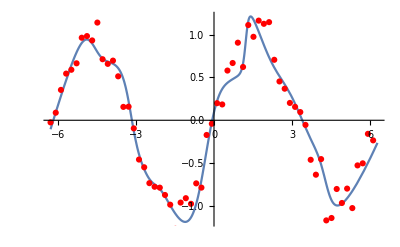

```mathematica
c=Show[Plot[net2[x],{x,-2π,2π}],plot]
Export[NotebookDirectory[]<>"non_overfitted_data"<>".png",c,ImageResolution->150];
```

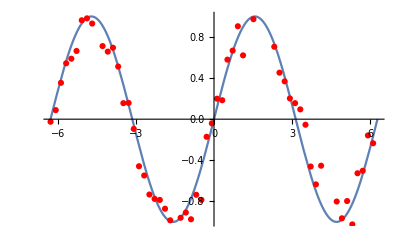

```mathematica
a=Show[{Plot[Sin[x],{x,-2π,2π}],plot}]
Export[NotebookDirectory[]<>"original_data"<>".png",a,ImageResolution->150];
```

```mathematica
net3=NetTrain[net,train,ValidationSet->test]
```

NetChain[<>]

```mathematica
c2=Show[Plot[net3[x],{x,-2π,2π}],plot]
Export[NotebookDirectory[]<>"non_overfitted_data2"<>".png",c2,ImageResolution->150];
```

-Graphics-